```mathematica
Needs["PlotLegends`"]
```

LegendShadow::shdw: Symbol "LegendShadow" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

PlotLegend::shdw: Symbol "PlotLegend" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

```mathematica
nmax = 15;
α = 0.6;
c = 2.997 10^8;hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
ω = c 2 Pi/λ;
λLat = 532 10^-9;
Γ = 1.84 10^6;
ωLat = c * 2 Pi / (λLat);
IntensityLat = 1 /(10^-4);(*from other simulation*)
kb = 1.38066 10^-23;
ω0 = 1.3 10^6;
Ωfree = 2 Pi 30.6 10^3;
ΩRm1 = Sqrt[2 Pi 30.6 10^3];
ΩRm2 = Sqrt[2 Pi 30.6 10^3];
ΔRm = 10^9;
ΔR = 10^12;
(*lattice params*)
a = 532 10^-9;
σ = 0.1 *3 * (265 10^-12)^2/(2 Pi);
ρ = 1/a^2;
RCs = 500;
Dr[n_,nt_]:= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η 1)^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η 1)^2]Exp[-η^2/2];
```

```mathematica
Calculation of Scattering Rates Γeff(n)
```

```mathematica
Clear[P1list,P2list];
P1list = {};
P2list = {};
P3list = {};
tab = Table[
(*alpha factor to be guessed /measured*)
δ1 = 1;
δ2 = 1;
η = 0.2;
Ω1 = 50 2 Pi 10^3;
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
Int = 0.6 10^-3/(10^-4);
h = 2 Pi *hbar;
;ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];

H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun3=ρ33/.First[sol];
fun1=ρ11/.First[sol];
fun2 = ρ22 /. First[sol];
expsol = Solve[Re[fun3[4 10^-5  ]] == Re[fun3[1 10^-5 ]] Exp[-l 3 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
AppendTo[P1list, Re[fun1[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];
AppendTo[P2list, Re[fun2[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];
AppendTo[P3list, Re[fun3[1 10^-5 ]] /(Re[fun1[1 10^-5 ]] +Re[fun2[1 10^-5 ]] +Re[fun3[1 10^-5 ]]  )];
{n,lam},{n,0,15}]
Γscatt = tab[[All, 2]]
P1list
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

{{0,0},{1,71289.},{2,141868.},{3,208622.},{4,269385.},{5,321625.},{6,362704.},{7,391025.},{8,407470.},{9,414540.},{10,415504.},{11,412956.},{12,408538.},{13,403115.},{14,397096.},{15,390631.}}

{0,71289.,141868.,208622.,269385.,321625.,362704.,391025.,407470.,414540.,415504.,412956.,408538.,403115.,397096.,390631.}

{1.,0.913446,0.834965,0.762834,0.695124,0.633053,0.580301,0.538549,0.505567,0.47784,0.453576,0.43312,0.417708,0.408214,0.404587,0.405863}

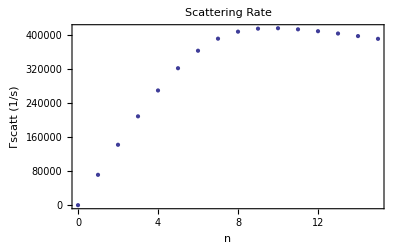

```mathematica
ListPlot[tab, FrameLabel-> {"n","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate", Frame-> True]
```

```mathematica
(Plots: Scattering Rate As a Function of Raman and Repump Coupling strengths.)
```

```mathematica
tabrepump =Table[ Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
Ω1 = 50 2 Pi 10^3;
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;
(*ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];*)
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-5}, MaxSteps-> 1000000];
fun=ρ33/.First[sol];
expsol = Solve[Re[fun[8 10^-5  ]] == Re[fun[5 10^-5 ]] Exp[-l  3 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
{ΩR,lam},{ΩR,0,4 10^6, 0.5 10^5}],{n,0,15}];
```

Set::write: Tag Times in 0\ 485760. is Protected.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Set::write: Tag Times in 0\ 485760. is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

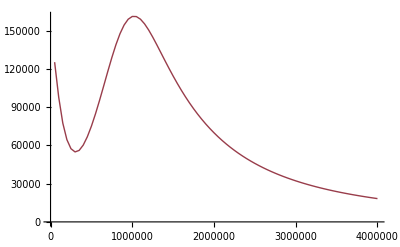
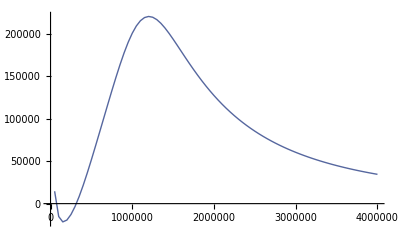
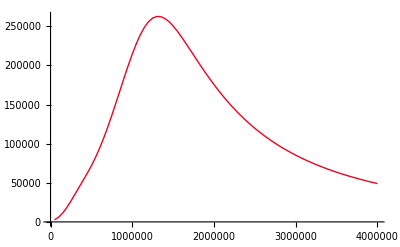
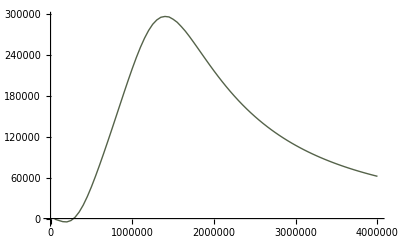
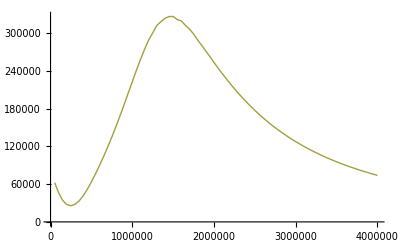
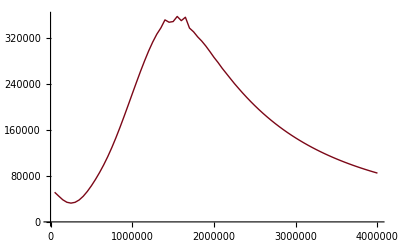
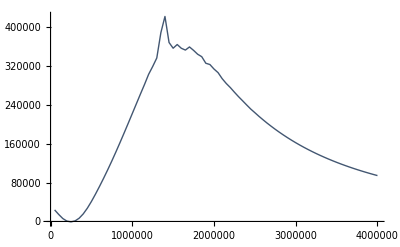
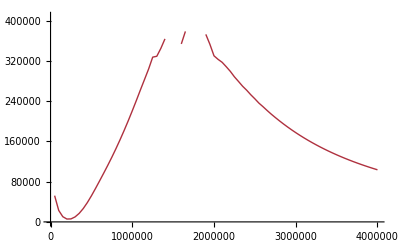

```mathematica
repumplots = Table[ListLinePlot[tabrepump[[n]], PlotStyle-> ColorData[n,"ColorList"]],{n,1,10}]
```

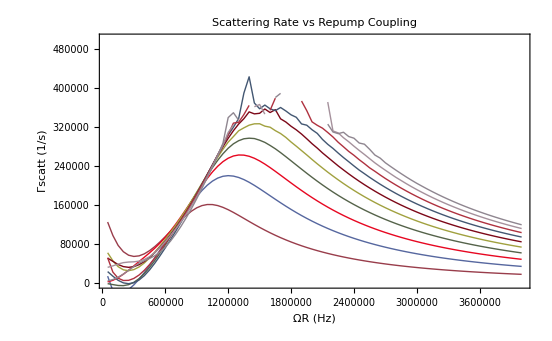

```mathematica
Show[repumplots , PlotRange -> {All,{0,500000}}, FrameLabel-> {"ΩR (Hz)","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate vs Repump Coupling", Frame-> True]
```

```mathematica
tabraman=Table[ Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
(*Ω1 = 50 2 Pi 10^3;*)
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;
ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun=ρ33/.First[sol];
expsol = Solve[Re[fun[10 10^-5  ]] == Re[fun[3 10^-5 ]] Exp[-l  7 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la] Γ/Γo];
{Ω1,lam},{Ω1,0,2.5 10^6, 2 10^4}],{n,0,15}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00730591.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00719219.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00706502.

General::stop: Further output of NDSolve :: mxst will be suppressed during this calculation.

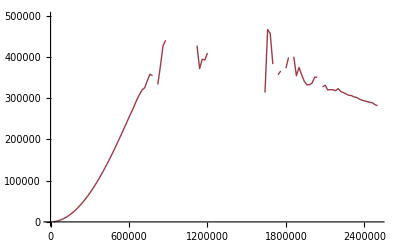
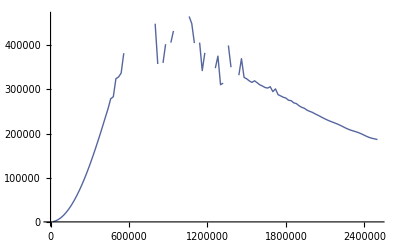
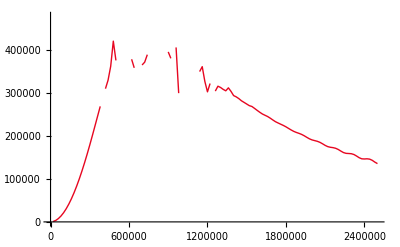
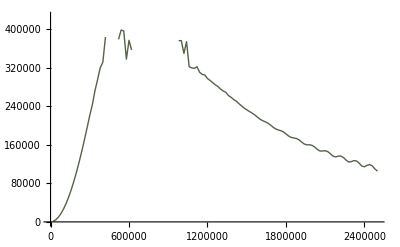
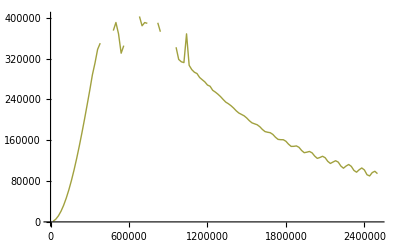
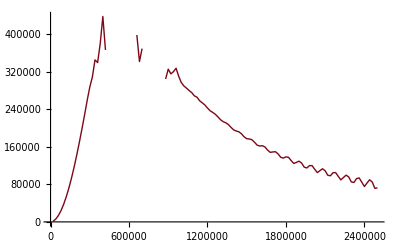
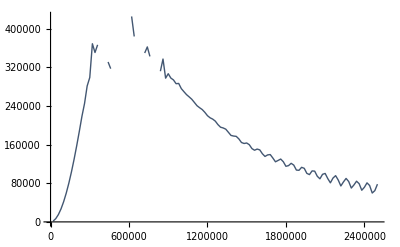
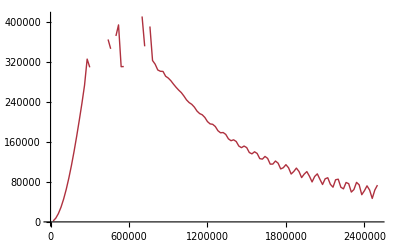

```mathematica
ramanplots = Table[ListLinePlot[tabraman[[n]], PlotStyle-> ColorData[n,"ColorList"]],{n,1,10}]
```

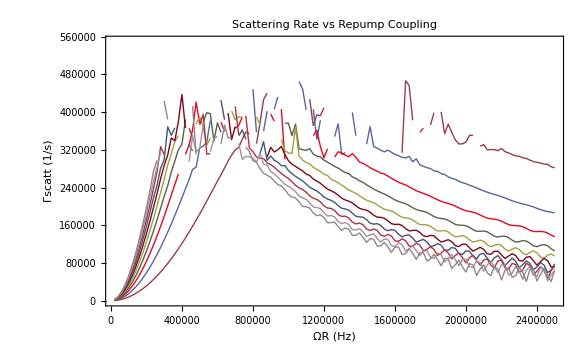

```mathematica
Show[ramanplots , PlotRange -> {All,{0,550000}}, FrameLabel-> {"ΩR (Hz)","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate vs Repump Coupling", Frame-> True]
```

```mathematica
Photon recoil
```

```mathematica
Γscatt;
pphoton = h / λ;
mCs = 132.90545 * 1.660539 10^-27 ;(*internet*)
Erecoil = pphoton^2/(2mCs);

Λreca= Γscatt * Erecoil;
Λrece= Γscatt * Erecoil;
Λrecarate= Γscatt * Erecoil    2/(3 kb) *10^3;
Λrecerate= Γscatt * Erecoil    2/(3 kb) *10^3
```

{0.,16.5009,32.8374,48.2884,62.3531,74.4447,83.9529,90.5082,94.3148,95.9513,96.1743,95.5845,94.562,93.3067,91.9135,90.4171}

```mathematica
Off-resonant scattering: Raman
```

```mathematica
Ephoton = h * c/λ;
ΛscRm =Table[ Γ    (ΩRm1^2 + ΩRm2^2)/(4 ΔRm^2) Ephoton ,{n,0,15}] 2/(3 kb)10^3
```

{3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234,3.7234}

```mathematica
Off-resonant scattering: Repump beam
```

```mathematica
ΛscRp = P1list* Γ ΩR^2/(4 ΔR^2)Ephoton 2/(3 kb)10^3
```

{24.2951,22.1923,20.2856,18.5331,16.8881,15.3801,14.0985,13.0841,12.2828,11.6092,11.0197,10.5227,10.1482,9.91759,9.82949,9.86048}

```mathematica
Lattice beams
```

```mathematica
(*ephoton not precise, should be average over all resonances*)
(*numerical value taken from last weeks simulartion*)
```

```mathematica
ΛscLat =  Table[1.00217872738179 10^-9 * IntensityLat 2*hbar ω 2/(3 kb) *10^3 ,{n,0,15}]
```

{421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916,421.916}

```mathematica
Off-Res Raman Couplings: Carrier transitions n-> n
```

```mathematica
Ωcarrier = Table[Ω1 (1-0.5 η^2(2n+1)),{n,0,15}];
Λcarrier = Table[P1list[[n+1]] ΩR^2/Γ Ωcarrier[[n+1]]^2/(4 ω0^2),{n,0,15}]2*Erecoil 2/(3 kb) *10^3
```

{8.85139,7.43872,6.23322,5.1998,4.30774,3.54968,2.92871,2.4321,2.02967,1.69288,1.40626,1.16401,0.962436,0.796091,0.657764,0.540139}

```mathematica
Off-Res Raman Couplings: Blue transitions
```

```mathematica
Ωblue = Table[Ω1 (Sqrt[n+1]),{n,0,15}]//N;

Λblue= Table[P1list[[n+1]] ΩR^2/Γ Ωblue[[n+1]]^2/(16 ω0^2),{n,0,15}]hbar ω0 2/(3 kb) *10^3
```

{32.9478,60.1922,82.5309,100.535,114.514,125.146,133.838,141.952,149.916,157.438,164.388,171.245,178.913,188.297,199.954,213.957}

```mathematica
Off-Res Raman Couplings: Doubly red
```

```mathematica
Ωdoublyred= Table[Ωcarrier[[1]]*η^2*Sqrt[(n-1)*n],{n,0,15}]//N;

Λdoublyred = -Table[P1list[[n+1]] ΩR^2/Γ Ωdoublyred[[n+1]]^2/(4 ω0^2),{n,0,15}]hbar ω0 2/(3 kb) *10^3
```

{0.,0.,-0.338187,-0.926916,-1.68928,-2.56407,-3.5256,-4.58072,-5.73357,-6.96745,-8.26706,-9.64851,-11.1662,-12.8965,-14.9122,-17.2607}

```mathematica
Rescattering
```

```mathematica
Λresc = Table[(P1list[[n+1]]α+P2list[[n+1]](1-α)) 1.00217872738179 10^9 (σ ρ)/2 Log[RCs],{n,0,15}]*2/(3 kb) *10^3 *2* Erecoil
```

{0.0170786,0.0156004,0.01426,0.0130282,0.0118718,0.0108117,0.00991074,0.00919768,0.00863438,0.00816085,0.00774645,0.0073971,0.00713387,0.00697173,0.00690979,0.00693158}

```mathematica
Repumping of state 2
```

```mathematica
Γ2s = ΩR^2 Γ/(Γ^2+4 δ2^2);
ΛRepump = Table[P2list[[n+1]] * Γ2s *2* Erecoil,{n,0,15}] 2/(3 kb) *10^3
```

{0.,30.547,56.9323,80.5405,102.504,122.793,141.094,158.036,174.687,191.212,206.599,219.454,228.815,234.491,236.99,237.26}

```mathematica
Cooling Rate
```

```mathematica
Λcool = -Table[P3list[[n+1]] α Abs[Dr[n-1,n-1]]^2*Γ,{n,0,15}] 2/(3 kb) *10^3 hbar ω0;
Λcool[[1]] = 0;
Λcool
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

{0,-446.61,-807.235,-1087.28,-1298.4,-1439.96,-1498.52,-1471.53,-1381.71,-1263.78,-1144.09,-1033.69,-933.124,-839.19,-749.113,-661.885}

```mathematica
Generate table
```

```mathematica
TableOfValues2=MapThread[Prepend,{{{"n = 0","n=1","n=2","n=3","n=4","n=5","n=6","n=7","n=8","n=9","n=10"},Λrecarate, Λrecerate,Λcarrier ,Λblue  ,ΛscRm ,ΛscRp ,Λresc,ΛscLat, Λdoublyred,Λcool},{"μK/ms","Λrecarate", "Λrecerate","Λcarrier" ,"Λblue"  ,"ΛscRm" ,"ΛscRp" ,"Λresc","ΛscLat","Λdoublyred","Λcool"}}];
Grid[TableOfValues2[[All,{1,2,3,6,8,10,12}]],ItemStyle->{Automatic,{1->{Bold,14}}},Frame->{All,1->True},Background->{None,{{LightOrange,LightGray}}}]
```

μK/ms | n = 0 | n=1 | n=4 | n=6 | n=8 | n=10
Λrecarate | 0. | 16.5009 | 62.3531 | 83.9529 | 94.3148 | 96.1743
Λrecerate | 0. | 16.5009 | 62.3531 | 83.9529 | 94.3148 | 96.1743
Λcarrier | 8.85139 | 7.43872 | 4.30774 | 2.92871 | 2.02967 | 1.40626
Λblue | 32.9478 | 60.1922 | 114.514 | 133.838 | 149.916 | 164.388
ΛscRm | 3.7234 | 3.7234 | 3.7234 | 3.7234 | 3.7234 | 3.7234
ΛscRp | 24.2951 | 22.1923 | 16.8881 | 14.0985 | 12.2828 | 11.0197
Λresc | 0.0170786 | 0.0156004 | 0.0118718 | 0.00991074 | 0.00863438 | 0.00774645
ΛscLat | 421.916 | 421.916 | 421.916 | 421.916 | 421.916 | 421.916
Λdoublyred | 0. | 0. | -1.68928 | -3.5256 | -5.73357 | -8.26706
Λcool | 0 | -446.61 | -1298.4 | -1498.52 | -1381.71 | -1144.09

```mathematica
Rate equation
```

```mathematica
Matrix Elements (from seperate notebook)
```

```mathematica
Matd ={{1.5337604188090186+0. ⅈ,0.11966389269178948+0. ⅈ,0.01156800726156411+0. ⅈ,0.001411048591966118+0. ⅈ,0.00021468875392546886+0. ⅈ,0.00003846590032110959+0. ⅈ,7.807444535791458*^-6+0. ⅈ,1.752707152273474*^-6+0. ⅈ,4.2781137299856986*^-7+0. ⅈ,1.1209643791990949*^-7+0. ⅈ,3.1223296738263093*^-8+0. ⅈ,9.17405856060743*^-9+0. ⅈ,2.8254571391355983*^-9+0. ⅈ,9.063420222659191*^-10+0. ⅈ,2.9795875404897314*^-10+0. ⅈ,9.98857424257307*^-11+0. ⅈ},{0.11966389269178945+0. ⅈ,1.317568647948566+0. ⅈ,0.19728890211322309+0. ⅈ,0.02709648524859807+0. ⅈ,0.004119013838066189+0. ⅈ,0.0007356294336309946+0. ⅈ,0.00014937501756307666+0. ⅈ,0.00003353670260266542+0. ⅈ,8.185543191506932*^-6+0. ⅈ,2.144799442424796*^-6+0. ⅈ,5.974130813190523*^-7+0. ⅈ,1.755324238013795*^-7+0. ⅈ,5.40610523196523*^-8+0. ⅈ,1.7341549846251833*^-8+0. ⅈ,5.701011876762306*^-9+0. ⅈ,1.91116989427912*^-9+0. ⅈ},{0.011568007261564112+0. ⅈ,0.19728890211322322+0. ⅈ,1.1551404700774563+0. ⅈ,0.24927288605279438+0. ⅈ,0.04356765819011158+0. ⅈ,0.007783908963170216+0. ⅈ,0.0015734879499190568+0. ⅈ,0.0003534581650443352+0. ⅈ,0.0000862856998746892+0. ⅈ,0.000022607566015886554+0. ⅈ,6.297096093130969*^-6+0. ⅈ,1.85022663363369*^-6+0. ⅈ,5.698386802326275*^-7+0. ⅈ,1.8279115840044158*^-7+0. ⅈ,6.009235940075373*^-8+0. ⅈ,2.01449696284489*^-8+0. ⅈ},{0.0014110485919661187+0. ⅈ,0.02709648524859808+0. ⅈ,0.2492728860527945+0. ⅈ,1.028984433463344+0. ⅈ,0.28450080953013546+0. ⅈ,0.059701502001262+0. ⅈ,0.012097002433284385+0. ⅈ,0.002701015397591902+0. ⅈ,0.0006597779765406222+0. ⅈ,0.00017291557893999224+0. ⅈ,0.000048159929335859994+0. ⅈ,0.000014150323113285317+0. ⅈ,4.3580951170707355*^-6+0. ⅈ,1.3979765171531368*^-6+0. ⅈ,4.595826661544421*^-7+0. ⅈ,1.5406750506838148*^-7+0. ⅈ},{0.00021468875392546886+0. ⅈ,0.004119013838066189+0. ⅈ,0.04356765819011159+0. ⅈ,0.28450080953013546+0. ⅈ,0.928685162557259+0. ⅈ,0.30823208183895656+0. ⅈ,0.07495341033531347+0. ⅈ,0.01682218579234278+0. ⅈ,0.004076931631546757+0. ⅈ,0.0010691978594604377+0. ⅈ,0.00029791975835811996+0. ⅈ,0.00008752511407614463+0. ⅈ,0.000026955923255357564+0. ⅈ,8.64694464071561*^-6+0. ⅈ,2.842671030081411*^-6+0. ⅈ,9.529573379349921*^-7+0. ⅈ},{0.000038465900321109594+0. ⅈ,0.000735629433630995+0. ⅈ,0.007783908963170215+0. ⅈ,0.059701502001261994+0. ⅈ,0.3082320818389565+0. ⅈ,0.8475752206230598+0. ⅈ,0.3237892281011723+0. ⅈ,0.08911042981100728+0. ⅈ,0.021789140423117807+0. ⅈ,0.005657588272601433+0. ⅈ,0.0015774155924708098+0. ⅈ,0.0004637270344278081+0. ⅈ,0.00014279856828211822+0. ⅈ,0.00004580527740505525+0. ⅈ,0.000015058693809651374+0. ⅈ,5.048180033411273*^-6+0. ⅈ},{7.807444535791461*^-6+0. ⅈ,0.00014937501756307674+0. ⅈ,0.001573487949919057+0. ⅈ,0.012097002433284385+0. ⅈ,0.0749534103353135+0. ⅈ,0.3237892281011725+0. ⅈ,0.7811464707560863+0. ⅈ,0.33338084531452916+0. ⅈ,0.10211370537428019+0. ⅈ,0.026878287380940908+0. ⅈ,0.007402187503414653+0. ⅈ,0.0021771337418679563+0. ⅈ,0.0006710462735876647+0. ⅈ,0.00021521500142190764+0. ⅈ,0.00007074810600626288+0. ⅈ,0.000023717744775128895+0. ⅈ},{1.7527071522734678*^-6+0. ⅈ,0.00003353670260266529+0. ⅈ,0.0003534581650443339+0. ⅈ,0.002701015397591892+0. ⅈ,0.016822185792342723+0. ⅈ,0.089110429811007+0. ⅈ,0.3333808453145265+0. ⅈ,0.7262158098272709+0. ⅈ,0.3385373835587837+0. ⅈ,0.11397570994644733+0. ⅈ,0.03200704994925855+0. ⅈ,0.00927470132716163+0. ⅈ,0.002859180131807137+0. ⅈ,0.000918171364983374+0. ⅈ,0.00030177832369475486+0. ⅈ,0.0001011579210327856+0. ⅈ},{4.278113729983148*^-7+0. ⅈ,8.185543191502053*^-6+0. ⅈ,0.00008628569987463771+0. ⅈ,0.0006597779765402284+0. ⅈ,0.004076931631544328+0. ⅈ,0.021789140423104984+0. ⅈ,0.10211370537421564+0. ⅈ,0.3385373835585461+0. ⅈ,0.6804546454268016+0. ⅈ,0.3403570125912493+0. ⅈ,0.12474014931464827+0. ⅈ,0.03711876564169128+0. ⅈ,0.011243051013147945+0. ⅈ,0.003609227723067272+0. ⅈ,0.0011883209035745655+0. ⅈ,0.00039825800456630965+0. ⅈ},{1.120964379234697*^-7+0. ⅈ,2.1447994424929174*^-6+0. ⅈ,0.00002260756601660457+0. ⅈ,0.000172915578945483+0. ⅈ,0.0010691978594944236+0. ⅈ,0.005657588272781529+0. ⅈ,0.02687828738177181+0. ⅈ,0.11397570995016162+0. ⅈ,0.34035701260873874+0. ⅈ,0.6421081777559666+0. ⅈ,0.33965105849336+0. ⅈ,0.13446087741391782+0. ⅈ,0.04217008287886575+0. ⅈ,0.01326391011603635+0. ⅈ,0.004361997966833031+0. ⅈ,0.0014651675316673044+0. ⅈ},{3.122329675986239*^-8+0. ⅈ,5.97413081732325*^-7+0. ⅈ,6.297096097487105*^-6+0. ⅈ,0.000048159929369172634+0. ⅈ,0.00029791975856427385+0. ⅈ,0.0015774155935634271+0. ⅈ,0.007402187508477785+0. ⅈ,0.03200704997149804+0. ⅈ,0.12474014941796335+0. ⅈ,0.3396510585601643+0. ⅈ,0.6098187799161146+0. ⅈ,0.33702900086964144+0. ⅈ,0.14317654986475595+0. ⅈ,0.04707371964892928+0. ⅈ,0.015126255653191152+0. ⅈ,0.005070508818816466+0. ⅈ},{9.174057921928472*^-9+0. ⅈ,1.7553241158117873*^-7+0. ⅈ,1.8502265048249378*^-6+0. ⅈ,0.000014150322128155827+0. ⅈ,0.00008752510798286732+0. ⅈ,0.0004637270021552676+0. ⅈ,0.0021771335901127928+0. ⅈ,0.009274700679088385+0. ⅈ,0.03711876313733161+0. ⅈ,0.13446086808844626+0. ⅈ,0.33702895733111793+0. ⅈ,0.5824957164328187+0. ⅈ,0.33290562230056575+0. ⅈ,0.15074114864366317+0. ⅈ,0.05119512480852333+0. ⅈ,0.01672187286026799+0. ⅈ},{2.825456475273183*^-9+0. ⅈ,5.406103961760106*^-8+0. ⅈ,5.698385463442789*^-7+0. ⅈ,4.358094093116586*^-6+0. ⅈ,0.000026955916922223944+0. ⅈ,0.00014279853471204797+0. ⅈ,0.0006710461159768814+0. ⅈ,0.002859179467065056+0. ⅈ,0.011243048285669788+0. ⅈ,0.04217007180790023+0. ⅈ,0.14317654919757994+0. ⅈ,0.3329053066608716+0. ⅈ,0.55907209674702+0. ⅈ,0.32716812281399343+0. ⅈ,0.15522945513986833+0. ⅈ,0.05409734531798155+0. ⅈ},{9.064423695639196*^-10+0. ⅈ,1.7343469847463798*^-8+0. ⅈ,1.8281139645402593*^-7+0. ⅈ,1.398131296335814*^-6+0. ⅈ,8.647902011455644*^-6+0. ⅈ,0.00004581034894537425+0. ⅈ,0.00021523882240935977+0. ⅈ,0.000918273052875275+0. ⅈ,0.0036096291691487177+0. ⅈ,0.013265355749100894+0. ⅈ,0.047078733140624704+0. ⅈ,0.15076313287588824+0. ⅈ,0.3271890722929206+0. ⅈ,0.5361782226800967+0. ⅈ,0.3151592705658968+0. ⅈ,0.15628111089847924+0. ⅈ},{2.971474821167179*^-10+0. ⅈ,5.685489356284483*^-9+0. ⅈ,5.992874197975165*^-8+0. ⅈ,4.583313294560272*^-7+0. ⅈ,2.8349311114019883*^-6+0. ⅈ,0.000015017692964316283+0. ⅈ,0.00007055546347695963+0. ⅈ,0.00030095660815248286+0. ⅈ,0.001185089539389658+0. ⅈ,0.004350096666569633+0. ⅈ,0.015084465392968276+0. ⅈ,0.05106265546864549+0. ⅈ,0.15487028036173794+0. ⅈ,0.3127411811338504+0. ⅈ,0.48953250536674353+0. ⅈ,0.3201766640445192+0. ⅈ},{1.0059323284565803*^-10+0. ⅈ,1.9247067044268376*^-9+0. ⅈ,2.0287656389157223*^-8+0. ⅈ,1.551587663614428*^-7+0. ⅈ,9.59707092004951*^-7+0. ⅈ,5.083935576613545*^-6+0. ⅈ,0.000023885771379760085+0. ⅈ,0.00010187430587434378+0. ⅈ,0.0004010695174030868+0. ⅈ,0.0014756523895217467+0. ⅈ,0.005107431178096411+0. ⅈ,0.01681750814919589+0. ⅈ,0.05446740212850906+0. ⅈ,0.16019427500990222+0. ⅈ,0.30446625806509053+0. ⅈ,0.26713032520432095+0. ⅈ}};
```

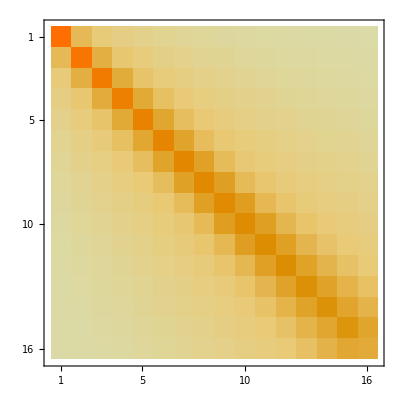

```mathematica
MatrixPlot[Matd]
```

```mathematica
Γheat = 0.1* Table[(Λrecarate[[n+1]]+ Λrecerate[[n+1]]+Λcarrier[[n+1]]+Λblue[[n+1]]  +ΛscRm[[n+1]] +ΛscRp[[n+1]] +Λresc[[n+1]]+ ΛscLat[[n+1]] +  Λdoublyred[[n+1]])α/(3 Erecoil)(2/(3 kb) *10^3)^-1,{n,0,15}] (*cheated*)
```

{42490.4,47392.2,51847.3,55781.4,59134.7,61871.5,64018.,65630.2,66772.5,67511.3,67962.3,68269.6,68574.6,68984.6,69557.4,70298.3}

```mathematica
Γeff[n_]:=Γscatt[[n]]
```

Rate Equation

```mathematica
Pm[t_]:= {P0[t],P1[t],P2[t],P3[t],P4[t],P5[t],P6[t],P7[t],P8[t],P9[t],P10[t],P11[t],P12[t],P13[t],P14[t],P15[t]};
Pm'[t]
Pmen = {P0,P1,P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15};
```

{P0'[t],P1'[t],P2'[t],P3'[t],P4'[t],P5'[t],P6'[t],P7'[t],P8'[t],P9'[t],P10'[t],P11'[t],P12'[t],P13'[t],P14'[t],P15'[t]}

```mathematica
Clear[Γeff, Matd, Γheat, α]
```

```mathematica
R = Table[+α(Γeff[n+1]*Matd[[n+1,nt]]+Γheat[[n+1]]*Matd[[n+1,nt+1]]), {n,0,nmax},{nt,0,nmax}] ;
For[i=1,i≤ nmax+1,i++,R[[i,i]] = R[[i,i]] -(Γeff[i]+ Γheat[[i]])];
For[i=1,i≤ nmax+1,i++,R[[i,1]] = α Γheat[[i]]*Matd[[i,1]]];
R[[1,1]] =-(Γeff[1]+ Γheat[[1]]) +  α Γheat[[1]]*Matd[[1,1]];
R //MatrixForm
```

(-3388.35+0. ⅈ | 3050.74+0. ⅈ | 294.918+0. ⅈ | 35.9736+0. ⅈ | 5.47333+0. ⅈ | 0.980659+0. ⅈ | 0.199045+0. ⅈ | 0.044684+0. ⅈ | 0.0109067+0. ⅈ | 0.00285781+0. ⅈ | 0.000796015+0. ⅈ | 0.000233886+0. ⅈ | 0.0000720329+0. ⅈ | 0.0000231065+0. ⅈ | 7.59623×10^-6+0. ⅈ | 2.54651×10^-6+0. ⅈ
3402.68+0. ⅈ | -76097.3+0. ⅈ | 61966.9+0. ⅈ | 9209.21+0. ⅈ | 1276.13+0. ⅈ | 197.102+0. ⅈ | 35.7129+0. ⅈ | 7.3429+0. ⅈ | 1.66724+0. ⅈ | 0.411112+0. ⅈ | 0.108728+0. ⅈ | 0.0305447+0. ⅈ | 0.00904536+0. ⅈ | 0.00280549+0. ⅈ | 0.000903867+0. ⅈ | 0.000298196+0. ⅈ
359.862+0. ⅈ | 7122.02+0. ⅈ | -140987.+0. ⅈ | 106081.+0. ⅈ | 22573.6+0. ⅈ | 3950.66+0. ⅈ | 711.522+0. ⅈ | 144.932+0. ⅈ | 32.7709+0. ⅈ | 8.048+0. ⅈ | 2.12027+0. ⅈ | 0.593572+0. ⅈ | 0.17522+0. ⅈ | 0.0541915+0. ⅈ | 0.0174287+0. ⅈ | 0.00574179+0. ⅈ
47.2262+0. ⅈ | 1083.51+0. ⅈ | 11734.6+0. ⅈ | -198762.+0. ⅈ | 138323.+0. ⅈ | 37609.9+0. ⅈ | 7877.88+0. ⅈ | 1604.62+0. ⅈ | 360.176+0. ⅈ | 88.3736+0. ⅈ | 23.2562+0. ⅈ | 6.50191+0. ⅈ | 1.9171+0. ⅈ | 0.592304+0. ⅈ | 0.190371+0. ⅈ | 0.0626838+0. ⅈ
7.61733+0. ⅈ | 180.846+0. ⅈ | 2211.58+0. ⅈ | 17136.2+0. ⅈ | -249585.+0. ⅈ | 161041.+0. ⅈ | 52479.3+0. ⅈ | 12711.7+0. ⅈ | 2863.64+0. ⅈ | 696.896+0. ⅈ | 183.386+0. ⅈ | 51.2586+0. ⅈ | 15.1032+0. ⅈ | 4.66372+0. ⅈ | 1.49848+0. ⅈ | 0.493276+0. ⅈ
1.42797+0. ⅈ | 34.7316+0. ⅈ | 430.919+0. ⅈ | 3718.39+0. ⅈ | 22963.4+0. ⅈ | -292551.+0. ⅈ | 175581.+0. ⅈ | 65791.3+0. ⅈ | 18005.+0. ⅈ | 4414.79+0. ⅈ | 1150.33+0. ⅈ | 321.617+0. ⅈ | 94.7889+0. ⅈ | 29.257+0. ⅈ | 9.3983+0. ⅈ | 3.09336+0. ⅈ
0.29989+0. ⅈ | 7.43669+0. ⅈ | 92.9463+0. ⅈ | 807.082+0. ⅈ | 5511.6+0. ⅈ | 28748.5+0. ⅈ | -326254.+0. ⅈ | 182800.+0. ⅈ | 76473.4+0. ⅈ | 23254.6+0. ⅈ | 6133.64+0. ⅈ | 1694.51+0. ⅈ | 499.568+0. ⅈ | 154.301+0. ⅈ | 49.5531+0. ⅈ | 16.3074+0. ⅈ
0.0690183+0. ⅈ | 1.73182+0. ⅈ | 21.7867+0. ⅈ | 189.287+0. ⅈ | 1296.12+0. ⅈ | 7455.74+0. ⅈ | 34034.5+0. ⅈ | -349842.+0. ⅈ | 183712.+0. ⅈ | 83914.+0. ⅈ | 28000.8+0. ⅈ | 7874.55+0. ⅈ | 2288.57+0. ⅈ | 706.962+0. ⅈ | 227.3+0. ⅈ | 74.7851+0. ⅈ
0.0171396+0. ⅈ | 0.432534+0. ⅈ | 5.45813+0. ⅈ | 47.5283+0. ⅈ | 324.64+0. ⅈ | 1869.69+0. ⅈ | 9418.09+0. ⅈ | 38528.+0. ⅈ | -364215.+0. ⅈ | 179995.+0. ⅈ | 88208.7+0. ⅈ | 31983.8+0. ⅈ | 9525.31+0. ⅈ | 2893.32+0. ⅈ | 930.+0. ⅈ | 306.479+0. ⅈ
0.00454067+0. ⅈ | 0.11476+0. ⅈ | 1.44922+0. ⅈ | 12.6273+0. ⅈ | 86.318+0. ⅈ | 495.106+0. ⅈ | 2495.93+0. ⅈ | 11302.1+0. ⅈ | 42135.3+0. ⅈ | -371387.+0. ⅈ | 173466.+0. ⅈ | 89926.+0. ⅈ | 35151.8+0. ⅈ | 11026.+0. ⅈ | 3475.75+0. ⅈ | 1144.28+0. ⅈ
0.0012732+0. ⅈ | 0.032145+0. ⅈ | 0.405716+0. ⅈ | 3.53372+0. ⅈ | 24.1548+0. ⅈ | 138.595+0. ⅈ | 695.095+0. ⅈ | 3150.55+0. ⅈ | 13066.+0. ⅈ | 44948.1+0. ⅈ | -373924.+0. ⅈ | 165772.+0. ⅈ | 89860.5+0. ⅈ | 37613.8+0. ⅈ | 12352.4+0. ⅈ | 3977.77+0. ⅈ
0.000375785+0. ⅈ | 0.0094632+0. ⅈ | 0.119281+0. ⅈ | 1.03806+0. ⅈ | 7.09125+0. ⅈ | 40.6815+0. ⅈ | 204.078+0. ⅈ | 919.344+0. ⅈ | 3818.47+0. ⅈ | 14704.8+0. ⅈ | 47121.1+0. ⅈ | -373858.+0. ⅈ | 157963.+0. ⅈ | 88659.8+0. ⅈ | 39446.7+0. ⅈ | 13369.7+0. ⅈ
0.000116253+0. ⅈ | 0.00291691+0. ⅈ | 0.0366975+0. ⅈ | 0.318993+0. ⅈ | 2.17736+0. ⅈ | 12.4829+0. ⅈ | 62.6132+0. ⅈ | 282.129+0. ⅈ | 1163.44+0. ⅈ | 4491.+0. ⅈ | 16227.8+0. ⅈ | 48793.1+0. ⅈ | -372507.+0. ⅈ | 150503.+0. ⅈ | 86583.3+0. ⅈ | 40276.1+0. ⅈ
0.0000375183+0. ⅈ | 0.0009371+0. ⅈ | 0.0117616+0. ⅈ | 0.102086+0. ⅈ | 0.696108+0. ⅈ | 3.98779+0. ⅈ | 19.989+0. ⅈ | 90.0676+0. ⅈ | 371.507+0. ⅈ | 1422.12+0. ⅈ | 5157.1+0. ⅈ | 17627.1+0. ⅈ | 50007.5+0. ⅈ | -370770.+0. ⅈ | 142730.+0. ⅈ | 82695.9+0. ⅈ
0.0000124013+0. ⅈ | 0.000308078+0. ⅈ | 0.0038557+0. ⅈ | 0.0334067+0. ⅈ | 0.227515+0. ⅈ | 1.3022+0. ⅈ | 6.52267+0. ⅈ | 29.3706+0. ⅈ | 121.164+0. ⅈ | 463.905+0. ⅈ | 1665.99+0. ⅈ | 5725.06+0. ⅈ | 18629.5+0. ⅈ | 49951.1+0. ⅈ | -371710.+0. ⅈ | 129997.+0. ⅈ
4.24292×10^-6+0. ⅈ | 0.000104759+0. ⅈ | 0.00130682+0. ⅈ | 0.0112994+0. ⅈ | 0.0768454+0. ⅈ | 0.43937+0. ⅈ | 2.19904+0. ⅈ | 9.89527+0. ⅈ | 40.7939+0. ⅈ | 156.244+0. ⅈ | 561.288+0. ⅈ | 1906.42+0. ⅈ | 6239.04+0. ⅈ | 19522.8+0. ⅈ | 50388.2+0. ⅈ | -378302.+0. ⅈ)

```mathematica
Total [Table[Sum[R[[k,j]],{j,1,16}],{k,1,16}]]
```

-570171.+0. ⅈ

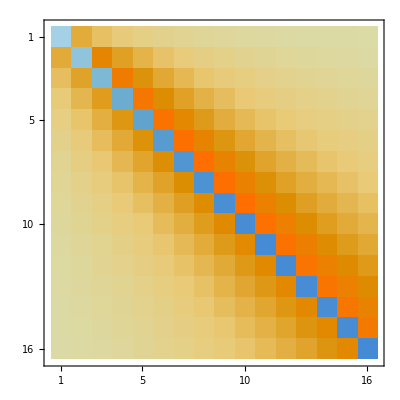

```mathematica
MatrixPlot[R]
```

```mathematica
system = Pm'[t] == R.Pm[t] ;
init=Pm[0]=={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

```mathematica
{P0[0],P1[0],P2[0],P3[0],P4[0],P5[0],P6[0],P7[0],P8[0],P9[0],P10[0],P11[0],P12[0],P13[0],P14[0],P15[0]}=={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

{P0[0],P1[0],P2[0],P3[0],P4[0],P5[0],P6[0],P7[0],P8[0],P9[0],P10[0],P11[0],P12[0],P13[0],P14[0],P15[0]}=={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{P0→InterpolatingFunction[{{0.,0.01}},<>],P1→InterpolatingFunction[{{0.,0.01}},<>],P2→InterpolatingFunction[{{0.,0.01}},<>],P3→InterpolatingFunction[{{0.,0.01}},<>],P4→InterpolatingFunction[{{0.,0.01}},<>],P5→InterpolatingFunction[{{0.,0.01}},<>],P6→InterpolatingFunction[{{0.,0.01}},<>],P7→InterpolatingFunction[{{0.,0.01}},<>],P8→InterpolatingFunction[{{0.,0.01}},<>],P9→InterpolatingFunction[{{0.,0.01}},<>],P10→InterpolatingFunction[{{0.,0.01}},<>],P11→InterpolatingFunction[{{0.,0.01}},<>],P12→InterpolatingFunction[{{0.,0.01}},<>],P13→InterpolatingFunction[{{0.,0.01}},<>],P14→InterpolatingFunction[{{0.,0.01}},<>],P15→InterpolatingFunction[{{0.,0.01}},<>]}}

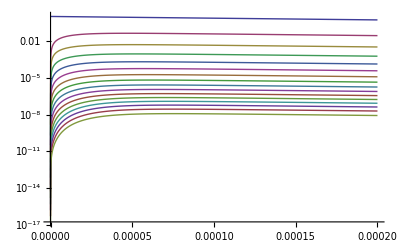

```mathematica
sol=NDSolve[LogicalExpand[Pm'[t]==R.Pm[t]&&init],Pmen,{t,0,0.01}]
LogPlot[Evaluate[{P0[t], P1[t],P2[t],P3[t],P4[t],P5[t],P6[t],P7[t],P8[t],P9[t],P10[t],P11[t],P12[t],P13[t],P14[t],P15[t]}/.sol],{t,0,0.0002}, PlotRange -> All, PlotLegend -> {0,1,2,3,4,5,6,7,8,9,10, 11,12,13,14, 15}, LegendShadow -> None]
```

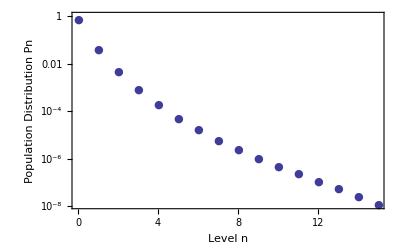

```mathematica
tel = 0.0001;
SteadyState = Table[
func = Pmen[[n+1]]/.First[sol];
steadyvalue = func[tel];
{n, steadyvalue},{n,0,15}];
ListLogPlot[SteadyState, Joined -> False, PlotMarkers -> {Automatic,Small}, Frame-> True, FrameLabel-> {"Level n", "Population Distribution Pn"}]
```

```mathematica
SteadySum = Sum[func  = Pmen[[n+1]]/.First[sol];
func[tel], {n,0, nmax}];
NormalizedSteadyState =Table[{n,SteadyState[[n+1]][[2]] / SteadySum },{n,0,15}]
```

```mathematica
{{0,0.893799676727197+0. ⅈ},{1,0.08620817764218629+0. ⅈ},{2,0.015032185723324428+0. ⅈ},{3,0.0034672396912133006+0. ⅈ},{4,0.0009734374133362995+0. ⅈ},{5,0.0003170163586800208+0. ⅈ},{6,0.00011616353602552123+0. ⅈ},{7,0.00004686163670297229+0. ⅈ},{8,0.000020450321459697134+0. ⅈ},{9,9.511118685544383*^-6+0. ⅈ},{10,4.649633425086806*^-6+0. ⅈ},{11,2.355695746075494*^-6+0. ⅈ},{12,1.215978046027865*^-6+0. ⅈ},{13,6.234189080553515*^-7+0. ⅈ},{14,3.018036670885262*^-7+0. ⅈ},{15,1.3330139672749573*^-7+0. ⅈ}}
```

{{0,0.8938+0. ⅈ},{1,0.0862082+0. ⅈ},{2,0.0150322+0. ⅈ},{3,0.00346724+0. ⅈ},{4,0.000973437+0. ⅈ},{5,0.000317016+0. ⅈ},{6,0.000116164+0. ⅈ},{7,0.0000468616+0. ⅈ},{8,0.0000204503+0. ⅈ},{9,9.51112×10^-6+0. ⅈ},{10,4.64963×10^-6+0. ⅈ},{11,2.3557×10^-6+0. ⅈ},{12,1.21598×10^-6+0. ⅈ},{13,6.23419×10^-7+0. ⅈ},{14,3.01804×10^-7+0. ⅈ},{15,1.33301×10^-7+0. ⅈ}}

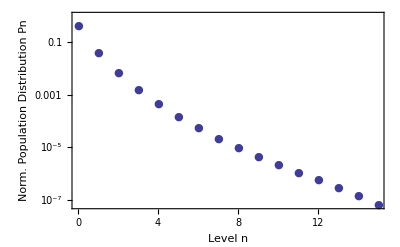

```mathematica
ListLogPlot[SteadyState, Joined -> False, PlotMarkers -> {Automatic,Small}, Frame-> True, FrameLabel-> {"Level n", "Norm. Population Distribution Pn"}]
```

```mathematica
Calculate average energy
```